```mathematica
c = ClusterClassify[{-10, -9, -8, -7, 5, 6, 7, 8}]
```

ClassifierFunction[…]

```mathematica
c[0]
```

1

```mathematica
c[0]
```

1

```mathematica
c[0, "Probabilities"]
```

<|1→0.999877,2→0.000123395|>

```mathematica
c[{-10, 0, 30}]
```

{2,1,1}

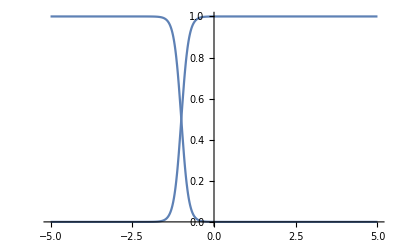

```mathematica
Plot[Values[c[x, "Probabilities"]], {x, -5, 5}]
```

```mathematica
colors = RandomColor[70]
```

{RGBColor[0.10507818371650668, 0.7779402547023742, 0.40592523310547346],RGBColor[0.021198034886289907, 0.41930772101660985, 0.6728141432735699],RGBColor[0.4992904928398485, 0.7406961635916165, 0.8509738281622976],RGBColor[0.48757770579811543, 0.5939339791488765, 0.6803334392793008],RGBColor[0.9416219807887138, 0.930558827599816, 0.009836821154149966],RGBColor[0.2338926625046014, 0.10824778187317552, 0.1083039421944394],RGBColor[0.8692426235479109, 0.16783919508666312, 0.6451360436486644],RGBColor[0.7959631248512078, 0.5479631725585445, 0.5904936306432043],RGBColor[0.1914086885378674, 0.4235745470319845, 0.029438738979705947],RGBColor[0.12970896160097123, 0.8046582038411303, 0.3883951041357514],RGBColor[0.45597948542171984, 0.1645112082548521, 0.05642068616906637],RGBColor[0.18604551491742138, 0.9086247507319458, 0.04144152588366379],RGBColor[0.7867808997013164, 0.04323130933604746, 0.5673169336779127],RGBColor[0.2634469466614551, 0.1141729389898507, 0.21546881071248492],RGBColor[0.39339126499884425, 0.08469184564159771, 0.8466570633562596],RGBColor[0.4515631090969894, 0.6524596779265934, 0.6174264562581464],RGBColor[0.48284651205827167, 0.6026520772667341, 0.7549995286060154],RGBColor[0.1878245311972575, 0.6695728588169119, 0.17525184878990596],RGBColor[0.9557926986783278, 0.5392823955190005, 0.1109463749702031],RGBColor[0.122212989673254, 0.8541321027583051, 0.5795717684198476],RGBColor[0.09237179128570472, 0.2211060325493015, 0.02409556005609459],RGBColor[0.7264185595839456, 0.12549143575675847, 0.5366637575735489],RGBColor[0.616467053952346, 0.04081496526809936, 0.8931562291180801],RGBColor[0.7937409965563729, 0.2722129480511828, 0.004540662563757181],RGBColor[0.5967690656568492, 0.8743797931639488, 0.592972620573748],RGBColor[0.661569919446678, 0.009348965767489448, 0.3785759847167769],RGBColor[0.24594161936074932, 0.7898369535191763, 0.5244411347258204],RGBColor[0.7165458787549777, 0.4704397675556362, 0.4984578723518285],RGBColor[0.9443706194786137, 0.8479621480242854, 0.039529359988129675],RGBColor[0.10872994934409319, 0.8963585710320923, 0.9364119437865721],RGBColor[0.6714618726070782, 0.19228867142673334, 0.08137637085960514],RGBColor[0.05700396524029938, 0.13487157240615555, 0.8648754109078667],RGBColor[0.291632431990283, 0.839924078003337, 0.08493069699833855],RGBColor[0.1126049961742297, 0.5384419309302984, 0.9995778640492172],RGBColor[0.05179931778037683, 0.981851410873956, 0.375387939243081],RGBColor[0.8335835656243153, 0.4661317764780688, 0.12504632496844148],RGBColor[0.8856645407851031, 0.3495844466763134, 0.8265239147958443],RGBColor[0.6632914798618539, 0.7466136360885711, 0.9254137176130026],RGBColor[0.9722699908107613, 0.24044077064747116, 0.9707932810657625],RGBColor[0.34901726609287764, 0.8021676160909144, 0.34819174980475087],RGBColor[0.19828409533028135, 0.8791618536078791, 0.26964599327069694],RGBColor[0.6493661285877128, 0.15083265954865888, 0.8960915773219886],RGBColor[0.4909776557221892, 0.22114122541577474, 0.59028957281243],RGBColor[0.8448466239983796, 0.8326554605722616, 0.8277304037761899],RGBColor[0.5093083128771287, 0.587657804928629, 0.8630687349150219],RGBColor[0.1737190622362743, 0.5134093153214263, 0.970768304510379],RGBColor[0.28264334200110075, 0.4291588649344362, 0.06456724533635927],RGBColor[0.060308659774971574, 0.12261616966965794, 0.14877586986199742],RGBColor[0.40695459260574696, 0.8863579202580438, 0.7864041506502006],RGBColor[0.09422016091078533, 0.1382893090713775, 0.3637838371114539],RGBColor[0.7534968462943057, 0.5622140840138283, 0.4087913716074254],RGBColor[0.5336526040929468, 0.8272241167617118, 0.5518014876737873],RGBColor[0.825346040874047, 0.8345861493659217, 0.5773014915739589],RGBColor[0.5326734576835443, 0.7467409115633858, 0.1809653364252246],RGBColor[0.5889765294598459, 0.09478981073581227, 0.47966805695901105],RGBColor[0.6619105395060365, 0.4765828156013303, 0.49372373108043366],RGBColor[0.09424535255861866, 0.2989974420125121, 0.15797951213300188],RGBColor[0.1212378886704919, 0.4982960638797256, 0.9959715059120207],RGBColor[0.21225846603071497, 0.4782910152401363, 0.665531261764595],RGBColor[0.24371785230671006, 0.8828729683773293, 0.39645505608359377],RGBColor[0.9354192504453149, 0.43241954361135404, 0.8992342070821406],RGBColor[0.90940948912055, 0.09942716525699935, 0.9540798806972197],RGBColor[0.44857264630082483, 0.8037632171825781, 0.41711346887424905],RGBColor[0.7128857072955839, 0.9704646865391697, 0.23611431167731012],RGBColor[0.9808833201328664, 0.746219177160778, 0.3799967630723784],RGBColor[0.5197778800616517, 0.9301002212695304, 0.7080251302649512],RGBColor[0.15438019996417984, 0.4438146369511802, 0.8237758464929268],RGBColor[0.6583319265079337, 0.8970679713384744, 0.9857111940674512],RGBColor[0.5399156900180531, 0.5643795958601452, 0.29996555597835073],RGBColor[0.11208575582308589, 0.22489761186045154, 0.9070479394636806]}

```mathematica
c = ClusterClassify[colors, 5]
```

ClassifierFunction[…]

```mathematica
c["Red"]
```

5

```mathematica
c2 = ClusterClassify[colors]
```

ClassifierFunction[…]

```mathematica
GatherBy[colors, c]
```

{{RGBColor[0.10507818371650668, 0.7779402547023742, 0.40592523310547346],RGBColor[0.1914086885378674, 0.4235745470319845, 0.029438738979705947],RGBColor[0.12970896160097123, 0.8046582038411303, 0.3883951041357514],RGBColor[0.18604551491742138, 0.9086247507319458, 0.04144152588366379],RGBColor[0.1878245311972575, 0.6695728588169119, 0.17525184878990596],RGBColor[0.122212989673254, 0.8541321027583051, 0.5795717684198476],RGBColor[0.09237179128570472, 0.2211060325493015, 0.02409556005609459],RGBColor[0.5967690656568492, 0.8743797931639488, 0.592972620573748],RGBColor[0.24594161936074932, 0.7898369535191763, 0.5244411347258204],RGBColor[0.291632431990283, 0.839924078003337, 0.08493069699833855],RGBColor[0.05179931778037683, 0.981851410873956, 0.375387939243081],RGBColor[0.34901726609287764, 0.8021676160909144, 0.34819174980475087],RGBColor[0.19828409533028135, 0.8791618536078791, 0.26964599327069694],RGBColor[0.28264334200110075, 0.4291588649344362, 0.06456724533635927],RGBColor[0.40695459260574696, 0.8863579202580438, 0.7864041506502006],RGBColor[0.5336526040929468, 0.8272241167617118, 0.5518014876737873],RGBColor[0.825346040874047, 0.8345861493659217, 0.5773014915739589],RGBColor[0.5326734576835443, 0.7467409115633858, 0.1809653364252246],RGBColor[0.09424535255861866, 0.2989974420125121, 0.15797951213300188],RGBColor[0.24371785230671006, 0.8828729683773293, 0.39645505608359377],RGBColor[0.44857264630082483, 0.8037632171825781, 0.41711346887424905],RGBColor[0.5197778800616517, 0.9301002212695304, 0.7080251302649512],RGBColor[0.5399156900180531, 0.5643795958601452, 0.29996555597835073]},{RGBColor[0.021198034886289907, 0.41930772101660985, 0.6728141432735699],RGBColor[0.4992904928398485, 0.7406961635916165, 0.8509738281622976],RGBColor[0.48757770579811543, 0.5939339791488765, 0.6803334392793008],RGBColor[0.2338926625046014, 0.10824778187317552, 0.1083039421944394],RGBColor[0.7959631248512078, 0.5479631725585445, 0.5904936306432043],RGBColor[0.2634469466614551, 0.1141729389898507, 0.21546881071248492],RGBColor[0.4515631090969894, 0.6524596779265934, 0.6174264562581464],RGBColor[0.48284651205827167, 0.6026520772667341, 0.7549995286060154],RGBColor[0.7165458787549777, 0.4704397675556362, 0.4984578723518285],RGBColor[0.10872994934409319, 0.8963585710320923, 0.9364119437865721],RGBColor[0.1126049961742297, 0.5384419309302984, 0.9995778640492172],RGBColor[0.6632914798618539, 0.7466136360885711, 0.9254137176130026],RGBColor[0.8448466239983796, 0.8326554605722616, 0.8277304037761899],RGBColor[0.5093083128771287, 0.587657804928629, 0.8630687349150219],RGBColor[0.1737190622362743, 0.5134093153214263, 0.970768304510379],RGBColor[0.060308659774971574, 0.12261616966965794, 0.14877586986199742],RGBColor[0.09422016091078533, 0.1382893090713775, 0.3637838371114539],RGBColor[0.6619105395060365, 0.4765828156013303, 0.49372373108043366],RGBColor[0.1212378886704919, 0.4982960638797256, 0.9959715059120207],RGBColor[0.21225846603071497, 0.4782910152401363, 0.665531261764595],RGBColor[0.15438019996417984, 0.4438146369511802, 0.8237758464929268],RGBColor[0.6583319265079337, 0.8970679713384744, 0.9857111940674512]},{RGBColor[0.9416219807887138, 0.930558827599816, 0.009836821154149966],RGBColor[0.9443706194786137, 0.8479621480242854, 0.039529359988129675],RGBColor[0.7128857072955839, 0.9704646865391697, 0.23611431167731012]},{RGBColor[0.8692426235479109, 0.16783919508666312, 0.6451360436486644],RGBColor[0.7867808997013164, 0.04323130933604746, 0.5673169336779127],RGBColor[0.39339126499884425, 0.08469184564159771, 0.8466570633562596],RGBColor[0.7264185595839456, 0.12549143575675847, 0.5366637575735489],RGBColor[0.616467053952346, 0.04081496526809936, 0.8931562291180801],RGBColor[0.661569919446678, 0.009348965767489448, 0.3785759847167769],RGBColor[0.05700396524029938, 0.13487157240615555, 0.8648754109078667],RGBColor[0.8856645407851031, 0.3495844466763134, 0.8265239147958443],RGBColor[0.9722699908107613, 0.24044077064747116, 0.9707932810657625],RGBColor[0.6493661285877128, 0.15083265954865888, 0.8960915773219886],RGBColor[0.4909776557221892, 0.22114122541577474, 0.59028957281243],RGBColor[0.5889765294598459, 0.09478981073581227, 0.47966805695901105],RGBColor[0.9354192504453149, 0.43241954361135404, 0.8992342070821406],RGBColor[0.90940948912055, 0.09942716525699935, 0.9540798806972197],RGBColor[0.11208575582308589, 0.22489761186045154, 0.9070479394636806]},{RGBColor[0.45597948542171984, 0.1645112082548521, 0.05642068616906637],RGBColor[0.9557926986783278, 0.5392823955190005, 0.1109463749702031],RGBColor[0.7937409965563729, 0.2722129480511828, 0.004540662563757181],RGBColor[0.6714618726070782, 0.19228867142673334, 0.08137637085960514],RGBColor[0.8335835656243153, 0.4661317764780688, 0.12504632496844148],RGBColor[0.7534968462943057, 0.5622140840138283, 0.4087913716074254],RGBColor[0.9808833201328664, 0.746219177160778, 0.3799967630723784]}}

```mathematica
string = {"c", "a", "b", "rrrrr", "uuu7uuu", "uuuuu4u", "u5uuuuu"};
```

```mathematica
c = ClusterClassify[string]
```

ClassifierFunction[…]

```mathematica
components = c[string]
```

{3,3,3,2,1,1,1}

```mathematica
GatherBy[string, c]
```

{{c,a,b},{rrrrr},{uuu7uuu,uuuuu4u,u5uuuuu}}

```mathematica
images = {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-};
```

```mathematica
c = ClusterClassify[images, 4]
```

ClassifierFunction[…]

```mathematica
Pick[images, c[images], #]&/@ Range[4]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
images3D = Join[Image3D/@RandomReal[3, {3, 5, 5, 10, 2}], Image3D/@RandomReal[1, {3, 5, 5, 3, 2}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
RandomReal[3, {3, 5, 5, 10, 2}];
```

```mathematica
colors = RandomColor[20]
```

{RGBColor[0.7183517774394188, 0.44390452013544235, 0.24566214472376746],RGBColor[0.0695001787545253, 0.4350765098357119, 0.45036789536759736],RGBColor[0.5960248819713674, 0.5944275792825278, 0.728162295679909],RGBColor[0.5889983026687851, 0.5168474719955227, 0.27658488192530295],RGBColor[0.43478502342088454, 0.35238991211636894, 0.5169510033017077],RGBColor[0.8707015163349765, 0.41820024345201534, 0.6554565155176082],RGBColor[0.13713479841620413, 0.11127425949230574, 0.05638281612955631],RGBColor[0.8574825409632745, 0.4511407895876358, 0.3237072636293836],RGBColor[0.0029400680930524725, 0.2199427005535255, 0.9510620613845016],RGBColor[0.4240940406237952, 0.26828754761293583, 0.3707350742977622],RGBColor[0.22849868482109814, 0.5314034764229438, 0.11827744346995006],RGBColor[0.43721018364805175, 0.5721714477120117, 0.7870025013310009],RGBColor[0.11112000635141572, 0.9864446303896153, 0.2297291737524434],RGBColor[0.1473538926558935, 0.019430117781354728, 0.5601768493556378],RGBColor[0.584394944467916, 0.7235350191799266, 0.0076260950085726975],RGBColor[0.38320409038180747, 0.3560618396791464, 0.11864627506089565],RGBColor[0.4269612658116617, 0.5531619536663943, 0.810623791540654],RGBColor[0.4018397665931863, 0.47215895305378597, 0.8490325543384911],RGBColor[0.6334152218664546, 0.11772207134843882, 0.6672825771708466],RGBColor[0.22821478267719608, 0.9905655636593667, 0.7631407747751491]}

```mathematica
c = ClusterClassify[colors, 3]
```

ClassifierFunction[…]

```mathematica
c[colors]
```

{3,3,3,3,3,3,3,3,1,3,2,3,2,1,2,3,3,1,1,2}

```mathematica
strings = DictionaryLookup["q"~~___];
```

```mathematica
c = ClusterClassify[strings, 10]
```

ClassifierFunction[…]

```mathematica
newstrings = RandomSample[DictionaryLookup["a"~~___], 30]
```

{adventurism,alleviating,audio,anglicize,amniocenteses,affirmatively,avoidable,adjudication,abrasives,abolish,afterbirths,anthologies,asthmatic,aspen,ates,arising,admix,alleged,androgen,anapestics,ally,actioned,acyclic,ashcan,agglomerating,analytical,autocratically,anaphora,absurdly,acclimatized}

```mathematica
GatherBy[newstrings, c]
```

{{adventurism,alleviating,audio,anglicize,affirmatively,avoidable,adjudication,abrasives,abolish,afterbirths,anthologies,asthmatic,aspen,ates,arising,admix,alleged,androgen,anapestics,ally,actioned,acyclic,ashcan,agglomerating,analytical,anaphora,absurdly,acclimatized},{amniocenteses},{autocratically}}

```mathematica
data = Join[RandomReal[{-1, 1}, 20], RandomReal[{3, 4}, 20]];
```

```mathematica
c = ClusterClassify[data]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Numerical
Classes | ,,12
Method | GaussianMixture
Classifier memory | 34. kB
Training examples used | 40 examples
Training time | 1.41 s

```mathematica
ClassifierInformation[c, "MethodDescription"]
```

The GaussianMixture clustering algorithm corresponds to the variational inference applied to a Gaussian mixture model.

```mathematica
data = Join[RandomReal[{-1, 1}, {80, 2}], RandomReal[{2, 4}, {80, 2}]];
```

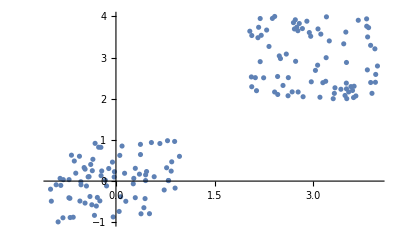

```mathematica
ListPlot[data]
```

```mathematica
c = ClusterClassify[data]
```

ClassifierFunction[…]

```mathematica
datatest = RandomReal[{-1, 4}, {2000, 2}];
```

```mathematica
decision = c[datatest];
```

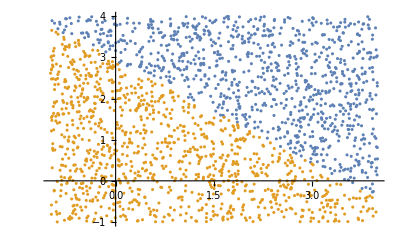

```mathematica
ListPlot[Pick[datatest, decision, #] &/@{1, 2}]
```

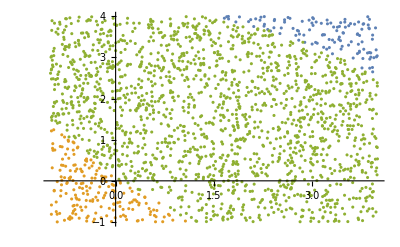

```mathematica
decision2 = c[datatest, IndeterminateThreshold->0.9 ];
ListPlot[Pick[datatest, decision2, #]&/@{1, 2, Indeterminate}]
```

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | NumericalVector (length: 2)
Classes | ,,12
Method | DBSCAN
Classifier memory | 58.6 kB
Training examples used | 160 examples
Training time | 3.32 s

```mathematica
ClassifierInformation[c, "MethodDescription"]
```

The density-based spatial clustering of applications with noise (DBSCAN) is a clustering algorithm that
groups together points that are closely packed together marking as outliers points that lie alone in low-density regions.

```mathematica
circle[r_, theta_] := {r Sin[theta], r Cos[theta]};
points = 
RandomVariate[MixtureDistribution[{1, 1}, {UniformDistribution[{{3/2, 2}, {0, 2 Pi}}],
UniformDistribution[{{0, 1/2}, {0, 2 Pi}}]}], 1000];
data = circle @@@ points;
```

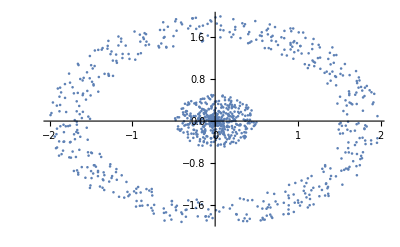

```mathematica
ListPlot[data, PlotRange->All]
```

```mathematica
c = ClusterClassify[data, 2]
```

ClassifierFunction[…]

```mathematica
d = ClusterClassify[data, 2, CriterionFunction-> "CalinskiHarabasz"]
```

ClassifierFunction[…]

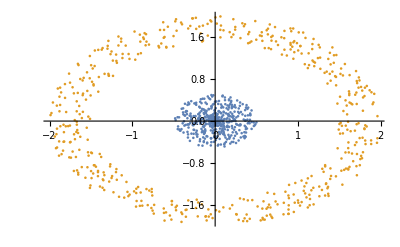

```mathematica
cCluster1 = Pick[data, c[data], 1];
cCluster2 = Pick[data, c[data], 2];
ListPlot[{cCluster1, cCluster2}]
```

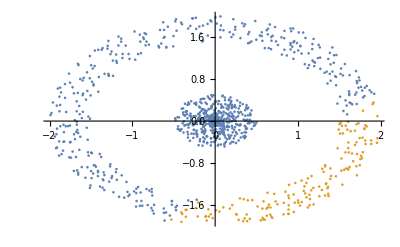

```mathematica
dCluster1 = Pick[data, d[data], 1];
dCluster2 = Pick[data, d[data], 2];
ListPlot[{dCluster1, dCluster2}]
```

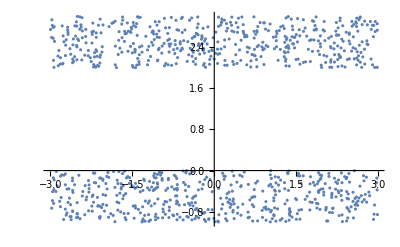

```mathematica
Dis = MixtureDistribution[{2, 2}, {UniformDistribution[{{-3, 3}, {-1, 0}}],
UniformDistribution[{{-3, 3}, {2, 3}}]}];
data = RandomVariate[Dis, 1000];
ListPlot[data, PlotRange-> All]
```

```mathematica
c = ClusterClassify[data]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c, "MethodDescription"]
```

The density-based spatial clustering of applications with noise (DBSCAN) is a clustering algorithm that
groups together points that are closely packed together marking as outliers points that lie alone in low-density regions.

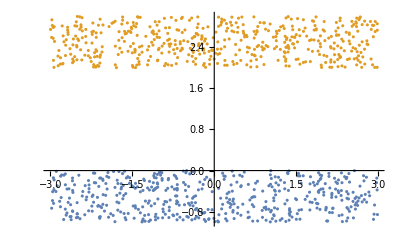

```mathematica
ListPlot[Pick[data, c[data], #]&/@{1, 2}]
```

ClassifierFunction[…]

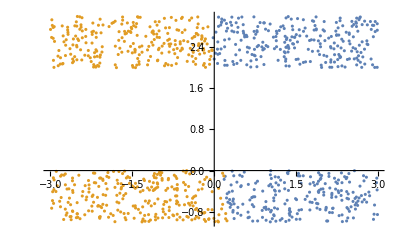

```mathematica
c = ClusterClassify[data, 2, Method -> "KMeans"]
ListPlot[Pick[data, c[data], #] &/@{1, 2}]
```

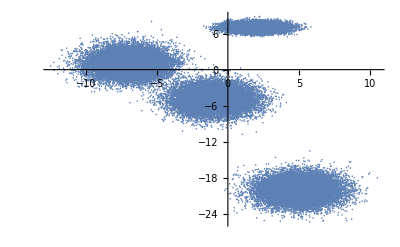

```mathematica
Dis=MixtureDistribution[{1,1,1,1},{MultinormalDistribution[{-1,-5},{{2,0},{0,2}}],MultinormalDistribution[{-7,1},{{2,0},{0,2}}],MultinormalDistribution[{2,7},{{1,0},{0,.2}}],MultinormalDistribution[{5,-20},{{2,0},{0,2}}]}];
data=RandomVariate[Dis,70000];
ListPlot[data,PlotRange->All]
```

```mathematica
{t, c} = ClusterClassify[data, 4, Method-> "KMedoids"] //AbsoluteTiming
```

{1.2029,ClassifierFunction[…]}

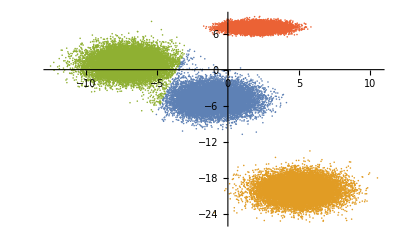

```mathematica
ListPlot[Pick[data, c[data], #]&/@Range[4]]
```

```mathematica
c = ClusterClassify[data, 4] //AbsoluteTiming
```

{6.05409,ClassifierFunction[…]}

```mathematica
colors = RandomColor[20]
```

{RGBColor[0.8202768825463487, 0.14522847101896086, 0.5954619087728545],RGBColor[0.7079259341104742, 0.46778353219203384, 0.3748272489924689],RGBColor[0.5312848902323279, 0.015176087198996102, 0.23896638042039275],RGBColor[0.3921040629369412, 0.799516131932603, 0.8728749372523019],RGBColor[0.28422368098062956, 0.564648055454543, 0.5900524979845898],RGBColor[0.13252262913198032, 0.2347657517825854, 0.08381730405360766],RGBColor[0.9900343179973514, 0.8863715247880593, 0.07836339759545163],RGBColor[0.40946457240630996, 0.41154211840997545, 0.3486205321669382],RGBColor[0.9054881613598098, 0.4134891537454384, 0.6855731787969714],RGBColor[0.36700442826708235, 0.16509772970499248, 0.9240342549252696],RGBColor[0.5180388452542806, 0.39055898731597605, 0.5767953358634765],RGBColor[0.08467833838131811, 0.9968684784910895, 0.63767413643145],RGBColor[0.1328254457981901, 0.08998622857729233, 0.7345702069011228],RGBColor[0.7524060559887857, 0.7427161914258018, 0.7534109522287673],RGBColor[0.4579967014407589, 0.9498891488755616, 0.29579507430634755],RGBColor[0.9667670079763506, 0.4936686827173091, 0.33019941863782876],RGBColor[0.38407761777709193, 0.9512732296262094, 0.3850045567628779],RGBColor[0.7822887384337911, 0.2360245774533507, 0.9531548945357378],RGBColor[0.9579367271624677, 0.6306173962575321, 0.703831788786514],RGBColor[0.9912387322492766, 0.4470814406582664, 0.9718425233955663]}

```mathematica
classifiers = Table[ClusterClassify[colors, 3], 5];
```

```mathematica
Counts[#[Green]&/@classifiers]
```

<|2→5|>

```mathematica
newClassifiers = Table[ClusterClassify[colors, 3, RandomSeeding->RandomInteger[20]], 5];
```

```mathematica
Count[#[Green]&/@newclassifiers]
```

Count[newclassifiers]

```mathematica
data = Join[Range[0, 5, 0.05], Range[25, 30, 0.05], {90}];
```

```mathematica
m = {{1, -1}, {1, 2}};
```

```mathematica
{u, w, v} = SingularValueDecomposition[N[m]]
```

{{{-0.289784,0.957092},{0.957092,0.289784}},{{2.30278,0.},{0.,1.30278}},{{0.289784,0.957092},{0.957092,-0.289784}}}

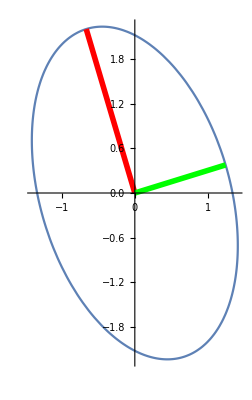

```mathematica
ParametricPlot[m.{Cos[t], Sin[t]}, {t, 0, 2 Pi}, Epilog -> {Thickness[0.01], {Red, Line[{{0, 0}, m.v[[All, 1]]}]}, {Green, Line[{{0, 0}, m.v[[All, 2]]}]}}]
```

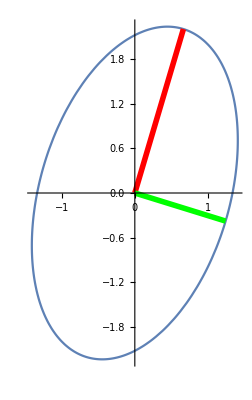

```mathematica
ParametricPlot[{Cos[t],Sin[t]}.m,{t,0,2 Pi},Epilog->{Thickness[0.01],{Red,Line[{{0,0},u[[All,1]].m}]},{Green,Line[{{0,0},u[[All,2]].m}]}}]
```

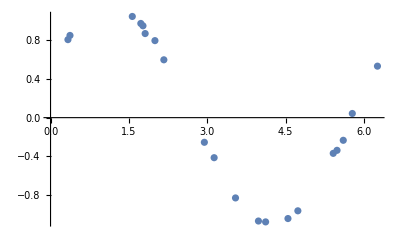

```mathematica
t = RandomReal[{0, 2 Pi}, 20];
y = Sin[t] + .5 Cos[t] + RandomReal[.1, 20];
data = Transpose[{t, y}];
ListPlot[data]
```

```mathematica
m = Map[Function[{s},  {1., Sin[s], Cos[s]}], t]
```

{{1.,-0.0248049,0.999692},{1.,0.980367,-0.197181},{1.,-0.999753,0.0222267},{1.,-0.7436,-0.668625},{1.,0.987655,-0.156644},{1.,0.00989241,-0.999951},{1.,0.826222,-0.563344},{1.,0.327096,0.944991},{1.,-0.628296,0.777974},{1.,0.909872,-0.41489},{1.,-0.388762,-0.921338},{1.,-0.716518,0.697568},{1.,0.971219,-0.238187},{1.,-0.485055,0.874484},{1.,-0.986033,-0.16655},{1.,-0.76523,0.643757},{1.,0.363706,0.931514},{1.,0.19572,-0.98066},{1.,0.999984,0.00572575},{1.,-0.828012,-0.56071}}

```mathematica
{u, w, v} = SingularValueDecomposition[m, 3]
```

{{{-0.224219,-0.157269,-0.29057},{-0.223525,0.276437,-0.115774},{-0.223578,-0.254067,0.172703},{-0.223164,-0.0851046,0.331432},{-0.22355,0.272127,-0.129071},{-0.222991,0.154304,0.295001},{-0.223293,0.293184,0.0200977},{-0.2242,-0.0606107,-0.337188},{-0.224058,-0.275245,-0.117246},{-0.223388,0.291706,-0.0387648},{-0.223023,0.0422819,0.342888},{-0.224005,-0.285223,-0.0777052},{-0.223499,0.28035,-0.102007},{-0.224123,-0.25389,-0.171372},{-0.223462,-0.22203,0.22612},{-0.22397,-0.289306,-0.0530866},{-0.224193,-0.0493755,-0.339734},{-0.223011,0.198049,0.256126},{-0.22365,0.250631,-0.179322},{-0.223226,-0.122648,0.314562}},{{4.47215,0.,0.},{0.,3.40983,0.},{0.,0.,2.8936}},{{-0.999996,0.00126145,0.00245038},{-0.000185283,0.856321,-0.516444},{-0.00274978,-0.516442,-0.856318}}}

```mathematica
x = v.((Transpose[u].y)/Diagonal[w])
```

{0.0425475,1.01089,0.49918}

```mathematica
Fit[data, {1, Sin[s], Cos[s]}, s]
```

0.0425475+0.49918 Cos[s]+1.01089 Sin[s]

```mathematica
m = RandomReal[1, {3, 4}];
a = RandomReal[1, {2, 4}];
{u, w, v} = SingularValueDecomposition[m]
```

{{{-0.853402,0.0544249,0.518404},{-0.436175,0.469982,-0.767378},{-0.285405,-0.880997,-0.377344}},{{1.9695,0.,0.,0.},{0.,0.703573,0.,0.},{0.,0.,0.535373,0.}},{{-0.652919,0.580537,-0.435878,-0.216064},{-0.401502,0.0599072,0.848947,-0.338375},{-0.360527,0.0740903,0.187271,0.910747},{-0.531519,-0.80864,-0.232873,-0.0967388}}}

```mathematica
Chop[m-u.w.ConjugateTranspose[v]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
{{u, ua}, {w, wa}, v} = SingularValueDecomposition[{m, a}]
```

{{{{-0.1995,0.443294,0.873894},{-0.102084,-0.896371,0.431391},{0.974566,-0.00314865,0.224079}},{{0.549031,-0.835802},{0.835802,0.549031}}},{{{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.863515,0.}},{{0.,0.,0.504322,0.},{0.,0.,0.,1.}}},{{-0.201569,-0.392948,1.50095,-0.698048},{-0.167105,0.390269,0.936105,-0.42004},{-0.0422153,0.0619328,0.828101,0.14786},{0.637266,0.0956187,1.16948,-0.141091}}}

```mathematica
Chop[a - ua.wa.ConjugateTranspose[v]]
```

{{0,0,0,0},{0,0,0,0}}

```mathematica
{m, a}
```

{{{0.998669,0.912746,0.660778,0.797771},{0.931927,0.0159433,0.257273,0.284883},{0.0952228,0.017049,0.118897,0.847047}},{{0.999026,0.610267,0.10571,0.441741},{0.24942,0.163966,0.430235,0.41549}}}

```mathematica
m = RandomReal[1, {2, 5}];
{u, w, v} = SingularValueDecomposition[m];
```

```mathematica
Sqrt[Eigenvalues[m.Transpose[m]]]
```

{1.76401,0.736187}

```mathematica
MatrixForm[w]
```

(1.76401 | 0. | 0. | 0. | 0.
0. | 0.736187 | 0. | 0. | 0.)

```mathematica
MatrixForm[Eigenvectors[m.Transpose[m]]]
```

(0.664812 | 0.747011
-0.747011 | 0.664812)

```mathematica
MatrixForm[Transpose[u]]
```

(-0.664812 | -0.747011
0.747011 | -0.664812)

```mathematica
MatrixForm[Eigenvectors[Transpose[m].m][[1;;2]]]
```

(-0.474751 | -0.290958 | -0.425517 | -0.353252 | -0.619761
0.488997 | 0.303346 | -0.664585 | -0.437672 | 0.188764)

```mathematica
MatrixForm[Transpose[v][[1;;2]]]
```

(-0.474751 | -0.290958 | -0.425517 | -0.353252 | -0.619761
-0.488997 | -0.303346 | 0.664585 | 0.437672 | -0.188764)

```mathematica
m = N[{{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}];
{u, w, v} = SingularValueDecomposition[m, Length[SingularValueList[m]]];
```

```mathematica
MatrixForm /@ {u, w, v}
```

{(-0.214837 | -0.887231
-0.520587 | -0.249644
-0.826338 | 0.387943),(16.8481 | 0.
0. | 1.06837),(-0.479671 | 0.776691
-0.572368 | 0.0756865
-0.665064 | -0.625318)}

```mathematica
winv = SparseArray[{i_, i_}-> 1 / w[[i, i]], Length[w]];
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
winv=SparseArray[{i_,i_}:>1/w[[i,i]],Length[w]];
```

```mathematica
MatrixForm[winv]
```

(0.0593539 | 0
0 | 0.936006)

```mathematica
mppi = v.winv.ConjugateTranspose[u]
```

{{-0.638889,-0.166667,0.305556},{-0.0555556,-6.93889×10^-17,0.0555556},{0.527778,0.166667,-0.194444}}

```mathematica
PseudoInverse[m]
```

{{-0.638889,-0.166667,0.305556},{-0.0555556,-6.93889×10^-17,0.0555556},{0.527778,0.166667,-0.194444}}

```mathematica
m = Outer[Times, {1, 2, 3}, {4, 5}]
```

{{4,5},{8,10},{12,15}}

```mathematica
PseudoInverse[m]
```

{{2/287,4/287,6/287},{5/574,5/287,15/574}}

```mathematica
m = Outer[Times, {1, 2, 3}, {4, 5}]
```

{{4,5},{8,10},{12,15}}

```mathematica
{u, w, v} = SingularValueDecomposition[m,1]
```

{{{1/(√14)},{√(2/7)},{3/(√14)}},{{√574}},{{4/(√41)},{5/(√41)}}}

```mathematica
{u[[All, 1]] == Normalize[{1, 2,3}], v[[All, 1]]==Normalize[{4, 5}]}
```

{True,True}

```mathematica
w[[1, 1]] == Norm[{1, 2, 3}]Norm[{4, 5}]
```

True